```mathematica
Plot3D[((
(-x+1)*Boole[1-y≤x]*Boole[x≤1]
+(x-1+2y )*Boole[1-2y≤x]*Boole[x≤1-y]
+(x+1-2y) *Boole[-1+y≤x]*Boole[x≤- 1+2y]
+(-x-1)*Boole[-1≤ x]*Boole[x≤ -1+y]
)*Boole[y>0]+
((x-1)*Boole[1-Abs[y]≤x]*Boole[x≤1]
+(-x+1-2*Abs[y])*Boole[1-2Abs[y]≤x]*Boole[x≤1-Abs[y]]
+(-x-1+2Abs[y])*Boole[-1+Abs[y]≤x]*Boole[x≤-1+2Abs[y]]
+(x+1)*Boole[-1≤x]*Boole[x≤ -1+Abs[y]]
)*Boole[y<0])
Boole[x≥    -1+2y&&x ≤  1+2y]
,{x,-1,1},{y,-1/2,1/2},PlotRange->{-1,1}]
```

-Graphics3D-

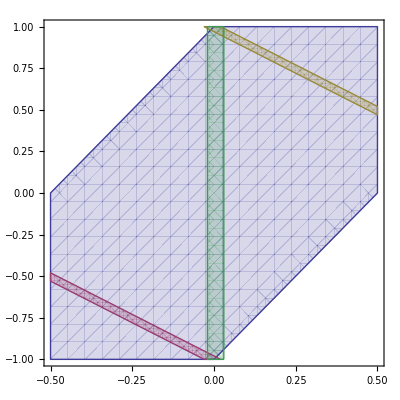

```mathematica
RegionPlot[{((y≥-1+2 x && y≤1)&&x>0)||(y≤-1)||((y≥-1&&y≤1+2x)&&x<0),((x<-1+Abs[y]+.02&& x>-1+Abs[ y]-.03))&&y<0,(x<1-y+.02&& x>1- y-.03),x>-.02&&x<.03},{x,-1/2,1/2},{y,-1,1}]
```

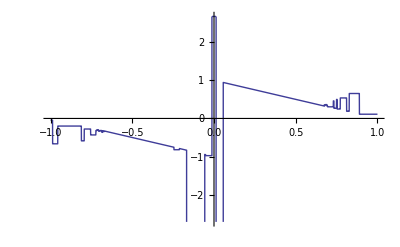

```mathematica
Plot[x/.Evaluate[Maximize[(
(-x+1)*Boole[1-y≤x]*Boole[x≤1]
+(x-1+2y )*Boole[1-2y≤x]*Boole[x≤1-y]
+(x+1-2y) *Boole[-1+y≤x]*Boole[x≤- 1+2y]
+(-x-1)*Boole[-1≤ x]*Boole[x≤ -1+y]
)*Boole[y>0]+
((x-1)*Boole[1-Abs[y]≤x]*Boole[x≤1]
+(-x+1-2*Abs[y])*Boole[1-2Abs[y]≤x]*Boole[x≤1-Abs[y]]
+(-x-1+2Abs[y])*Boole[-1+Abs[y]≤x]*Boole[x≤-1+2Abs[y]]
+(x+1)*Boole[-1≤x]*Boole[x≤ -1+Abs[y]]
)*Boole[y<0],x]][[2]][[1]],{y,-1,1}]
```